Definition of RK4

```mathematica
crkamat={{1/2},{0,1/2},{0,0,1}};
crkbvec={1/6,1/3,1/3,1/6};
crkcvec={1/2,1/2,1};
ClassicalRungeKuttaCoefficients[4,p_]:=N[{crkamat,crkbvec,crkcvec},p];
```

Compile the NDSolve parameter sweep

```mathematica
lorenz=Compile[
{{parameterList,_Real,1}},
Table[
sol=NDSolve[
{
x'[t]==10(y[t-13/28]-x[t]),
y'[t]==parameterList[[i]]*x[t] - y[t] - z[t]*x[t],
z'[t]==x[t]*y[t]-8/3  z[t],
x[t/;t≤0]==-8,
y[t/;t≤0]== -8+Sin[2π t],
z[t/;t≤0]==-8
},
x[t],
{t,0,10},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4,"Coefficients"->ClassicalRungeKuttaCoefficients},
StartingStepSize->0.001,
MaxSteps->10100
];
First@Evaluate[x[t]/.sol]/.t->10,
{i,1,Length[parameterList]}],
CompilationTarget->"C",
"RuntimeOptions"->"Speed"
]
```

CompiledFunction[…]

Run and Benchmark

```mathematica
nrOfParameters = 1024;
parameterList =N@Range[0,50,50/(nrOfParameters-1)];
runtime=Timing[endvals=lorenz[parameterList]];
runtime[[1]]
```

281.516

Export endvals

```mathematica
SetDirectory[NotebookDirectory[]];
Export["lorenz_endvals.txt",data=Transpose[{parameterList,endvals}],"Table"]
```

lorenz_endvals.txt

Plot endvals

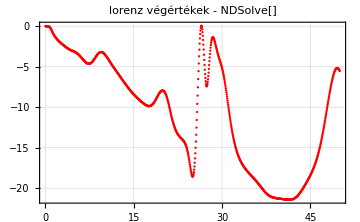

lorenz_endvals.png

```mathematica
plt=Show[
(*Plot[Evaluate[x[p][10]/.logistic1EndValues],{p,0,2},PlotStyle->Blue],*)
ListPlot[
data[[All,{1,2}]],
PlotStyle->Red,
FrameLabel->(MaTeX[#,Magnification->1.2]&)/@{"p","x(10)"},
PlotLabel->Style["lorenz végértékek - NDSolve[]",Black,14]
]
]
Export["lorenz_endvals.png",plt,ImageResolution->1000]
```